```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nodes=Import["n0.dat","Table"];triangles=Import["t0.dat","Table"]+1;
𝒦=MeshRegion[nodes,Triangle/@triangles];
```

```mathematica
HighlightMesh[𝒦,0,MeshCellLabel->{0->"Index"}]
HighlightMesh[𝒦,0,MeshCellLabel->{2->"Index"}];
```

-Graphics-

## Typical basis func

```mathematica
Subscript[𝒦, ϕ]=MeshRegion[
Append[Append[#,0.]&/@nodes,{nodes[[8,1]],nodes[[8,2]],1.}],
Flatten@{
Triangle/@Append[triangles,{
{10,9,14},
{9,14,2},
{6,14,7},
{7,14,1},
{2,6,14},
{1,14,10}
}],
Line[{1,14}],
Line[{10,14}],
Line[{9,14}],
Line[{2,14}],
Line[{6,14}],
Line[{7,14}]
}];
```

```mathematica
HighlightMesh[Subscript[𝒦, ϕ],Labeled[0, "Index"]]
```

-Graphics3D-

## Assembly illustration

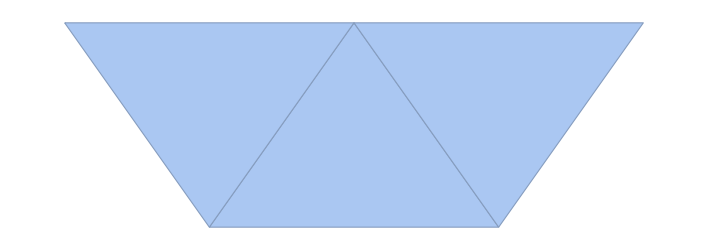

```mathematica
nodes ={{1/2,Sqrt[2]/2},{-1/2,Sqrt[2]/2},{3/2,Sqrt[2]/2},{1,0},{0,0}};
triangles={{5,4,1},{4,3,1},{2,5,1}};
 𝒦=MeshRegion[nodes,Triangle/@triangles]
HighlightMesh[𝒦,0,MeshCellLabel->{0->"Index",2->"Index"}];
```

## Refinement

```mathematica
nodes ={{1/2,Sqrt[2]/2},{-1/2,Sqrt[2]/2},{3/2,Sqrt[2]/2},{1,0},{0,0},{2,0}};
triangles={{5,4,1},{4,3,1},{2,5,1},{2,5,1},{4,3,6}};
 𝒦=MeshRegion[nodes,Triangle/@triangles];
HighlightMesh[𝒦,0,MeshCellLabel->{0->"Index",2->"Index"}]
```

-Graphics-

```mathematica
nodes ={
{1/2,Sqrt[2]/2},{-1/2,Sqrt[2]/2},{3/2,Sqrt[2]/2},{1,0},{0,0},{2,0},
{1/4,0}
};
triangles={{5,4,1},{4,3,1},{2,5,1},{2,5,1},{4,3,6}};
```

### MatrixPlot

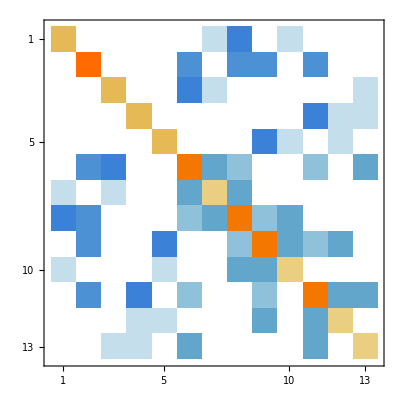

```mathematica
matrix=Import["matrixPlotCircle.dat","Table"];
MatrixPlot@matrix
```